```mathematica
f[x_,a_,z_]=1/(4a^3)*(4*a^2+(x-z)^2+(x-z-a)*Abs[x-z-a]-(x-z+a)*Abs[x-z+a])
```

1/(4 a^3)(4 a^2+(x-z)^2+(-a+x-z) Abs[-a+x-z]-(a+x-z) Abs[a+x-z])

```mathematica
Refine[f[z,a,z],{a>0}]
```

1/(2 a)

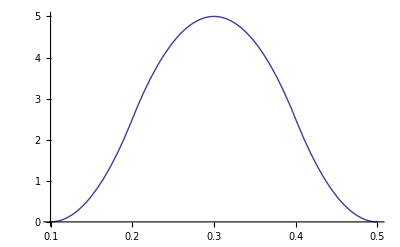

```mathematica
Plot[f[x,0.1,0.3],{x,0.1,0.5}]
```

```mathematica
Integrate[f[x,a,z],{x,z-2a,z-a}]+Integrate[f[x,a,z],{x,z-a,z}]+Integrate[f[x,a,z],{x,z,z+a}]+Integrate[f[x,a,z],{x,z+a,z+2a}]
```

16/3-(13 Abs[a])/(3 a)

```mathematica
fp[x_,a_,z_]=Simplify[D[f[x,a,z],x]]
```

-1/(4 a^3)(-2 x+2 z+Abs[a+x-z]-Abs[a-x+z]+(a-x+z) Abs'[-a+x-z]+(a+x-z) Abs'[a+x-z])

```mathematica
fpmod[x_,a_,z_]=Simplify[-1/(4 a^3)(-2 x+2 z+2Abs[a+x-z]-2Abs[a-x+z])]
```

1/(2 a^3)(x-z-Abs[a+x-z]+Abs[a-x+z])

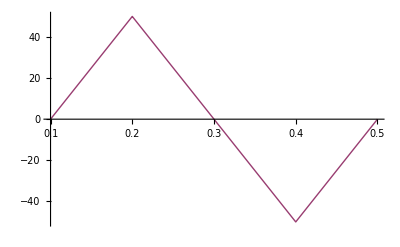

```mathematica
Plot[{fp[x,0.1,0.3],fpmod[x,0.1,0.3]},{x,0.1,0.5}]
```

```mathematica
Simplify[Refine[fp[z-a,a,z],{a>0}]]
```

-Abs'[-2 a]/(2 a^2)

```mathematica
weaknorm=Refine[Integrate[fpmod[x,a,z],{x,z-2a,z-a}]+Integrate[fpmod[x,a,z],{x,z-a,z}]+ Integrate[-fpmod[x,a,z],{x,z,z+a}]+Integrate[-fpmod[x,a,z],{x,z+a,z+2a}],{a>0}]
```

1/a

```mathematica
fpp[x_,a_,z_]=D[fpmod[x,a,z],x]
```

(1-Abs'[a+x-z]-Abs'[a-x+z])/(2 a^3)

```mathematica
fppmod[x_,a_,z_]= Simplify[(1-Sign[a+x-z]-Sign[a-x+z])/(2 a^3)]
```

-(-1+Sign[a+x-z]+Sign[a-x+z])/(2 a^3)

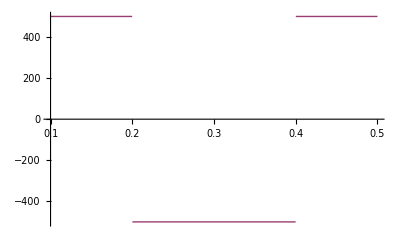

```mathematica
Plot[{fpp[x,0.1,0.3],fppmod[x,0.1,0.3]},{x,0.1,0.5}]
```

```mathematica
strongnorm=Refine[Integrate[fppmod[x,a,z],{x,z-2a,z-a}]+Integrate[-fppmod[x,a,z],{x,z-a,z+a}]+Integrate[fppmod[x,a,z],{x,z+a,z+2a}],{a>0, z>0}]
```

2/a^2